```mathematica
(*---第一步：几何结构与基本设置---*)
(* 原子坐标 (分数坐标)*)
latV={{-1.6848999334,1.6848999334,1.6848999334},{1.6848999334,-1.6848999334,1.6848999334},{1.6848999334,1.6848999334,-1.6848999334}};
fracPos={
{0.00,0.00,0.00},(*Y1*)
{0.50,0.75,0.25},(*H1*)
{0.50,0.25,0.75},(*H2*)
{0.25,0.50,0.75},(*H3*)
{0.75,0.50,0.25},(*H4*)
{0.75,0.25,0.50},(*H5*)
{0.25,0.75,0.50} (*H6*)
};
atomTypes={"Y","H","H","H","H","H","H"};
cartPos=fracPos.latV;
nAtoms=Length[fracPos];
orbCounts=<|"Y"->6,"H"->4|>;
totalDim=Total[orbCounts/@atomTypes];
startIndices=Accumulate[Prepend[orbCounts/@Most[atomTypes],0]]+1;
(*Most[atomTypes]*)
```

```mathematica
(*---第二步：紧束缚参数 (单位:eV)---*)
eYs=-2.0;eYd=2.5;
eHs=-6.0;eHp=4.0;

(*跳跃参数-示例初值，需根据DFT拟合*)
vssSigYH=-1.2;vspSigYH=1.5;vsdSigYH=-1.8;vpdSigYH=2.0;
vpdPiYH=-0.8;
vssSigHH=-0.8;vspSigHH=1.0;vppSigHH=1.2;
vppPiHH=-0.3;
```

```mathematica
(*---第三步：Slater-Koster 跳跃子矩阵函数---*)
SKBlock[t1_,t2_,distVec_,dist_]:=Module[
{l,m,n,mat,d1,d2},
{l,m,n}=distVec/dist;
d1=orbCounts[t1];
d2=orbCounts[t2];
mat=ConstantArray[0,{d1,d2}];
(*Y-H 相互作用*)
If[(t1=="Y"&&t2=="H")||(t1=="H"&&t2=="Y"),
Module[{vss,vsp,vsd,vpdS,vpdP,res,ll,mm,nn,vVec},
(*统一按 Y->H 的方向计算 l, m, n*)
vVec=If[t1=="Y",distVec,-distVec];
{ll,mm,nn}=vVec/dist;
vss=vssSigYH;
vsp=vspSigYH;
vsd=vsdSigYH;
vpdS=vpdSigYH;
vpdP=vpdPiYH;
res=ConstantArray[0,{6,4}];
(*Y(s,d)->H(s,p)*)
res[[1,1]]=vss;
res[[1,2;;4]]={ll,mm,nn}*vsp (*第1行，第2，3，4列填入数据*); 
res[[2,1]]=Sqrt[3] ll mm*vsd;
res[[3,1]]=Sqrt[3] mm nn*vsd;
res[[4,1]]=Sqrt[3] nn ll*vsd;
res[[5,1]]=Sqrt[3]/2 (ll^2-mm^2)*vsd;
res[[6,1]]=(nn^2-0.5 (ll^2+mm^2))*vsd;
(*p-d 部分公式略简，可按需补充完整*)
res[[2,2]]=Sqrt[3] ll^2 m vpdS+mm(1-2ll^2) vpdP;
res[[3,3]]=Sqrt[3] mm^2 nn vpdS+nn(1-2mm^2) vpdP;
res[[4,4]]=Sqrt[3] nn^2 ll vpdS+ll(1-2nn^2) vpdP;
If[t1=="Y",mat=res,mat=Transpose[res]]
]
];
(*H-H 相互作用*)
If[
t1=="H"&&t2=="H",
{l,m,n}=distVec/dist;
mat[[1,1]]=vssSigHH;
mat[[1,2;;4]]={l,m,n}*vspSigHH;
mat[[2;;4,1]]=-{l,m,n}*vspSigHH;
mat[[2,2]]=l^2 vppSigHH+(1-l^2) vppPiHH;
mat[[3,3]]=m^2 vppSigHH+(1-m^2) vppPiHH;
mat[[4,4]]=n^2 vppSigHH+(1-n^2) vppPiHH;
mat[[2,3]]=mat[[3,2]]=l m (vppSigHH-vppPiHH);
mat[[2,4]]=mat[[4,2]]=l n (vppSigHH-vppPiHH);
mat[[3,4]]=mat[[4,3]]=m n (vppSigHH-vppPiHH);
];

mat
];
```

```mathematica
(*---第四步：寻邻 (包含周期性)---*)
cutoff=2.5;
neighbors={};
Do[
distVec=(cartPos[[j]]+{dx,dy,dz}.latV)-cartPos[[i]];
dist=Norm[distVec];
If[
0.1<dist<cutoff,
AppendTo[neighbors,{i,j,{dx,dy,dz}}]
],{i,nAtoms},{j,nAtoms},{dx,-1,1},{dy,-1,1},{dz,-1,1}];
```

```mathematica
(*---第五步：构建哈密顿量---*)
Ham[k_List]:=Module[
{H,phase,block,i,j,R,distVec,dist,idxI,idxJ},
H=ConstantArray[0,{totalDim,totalDim}];

(*On-site*)
Do[
idx=startIndices[[i]];(*获取第 i 个原子的轨道在矩阵中的起始位置*)
If[
atomTypes[[i]]=="Y",
Do[(*如果是 Y 原子，填充 6 个轨道的能量：1个s 和 5个d, 填充的对角项*)
H[[idx+k1-1,idx+k1-1]]={eYs,eYd,eYd,eYd,eYd,eYd}[[k1]],{k1,6}
],

Do[(*如果是 H 原子，填充 4 个轨道的能量：1个s 和 3个p*)
H[[idx+k1-1,idx+k1-1]]={eHs,eHp,eHp,eHp}[[k1]],{k1,4}
]
],
{i,nAtoms}
];

(*Hopping*)
Do[{i,j,R}=nb;
distVec=(cartPos[[j]]+R.latV)-cartPos[[i]];(*计算两个原子间的实际空间矢量*)
dist=Norm[distVec];
block=SKBlock[atomTypes[[i]],atomTypes[[j]],distVec,dist];(*调用 SKBlock 函数计算这两个原子轨道之间的相互作用小矩阵*)
phase=Exp[I*2*Pi*(k.R)];(*布洛赫定理关键：计算相位因子 Exp(i*k·R)*)
idxI=startIndices[[i]];
idxJ=startIndices[[j]];
Do[
Do[
H[[idxI+r-1,idxJ+c-1]]+=block[[r,c]]*phase,{c,orbCounts[atomTypes[[j]]]}(*将计算出的小矩阵 block 乘以相位后，“贴”到大矩阵 H 的对应位置*)
],{r,orbCounts[atomTypes[[i]]]}
],{nb,neighbors}
];


(H+ConjugateTranspose[H])/2 (*保证厄米性*)
(* 物理要求：哈密顿量矩阵必须是厄米矩阵（$H=H^\dagger$），这样算出来的能量特征值（Eigenvalues）才一定是实数。
为什么要这一步：在数值计算中，由于只对邻居进行了单向遍历或者存在微小的浮点数误差，矩阵 $H$ 可能不是严格对称的。通过 (H+H†)/2 可以强制使其满足厄米性，消除数值噪音。*)
]
```

```mathematica
Print["\n--- Gamma 点能级简并度分析 ---"];
gammaEnergies=Eigenvalues[Ham[{0,0,0}]]
```

--- Gamma 点能级简并度分析 ---

{-26.1292,8.38314,8.38314,7.8,7.77986,7.77986,7.77986,-6.69692,-6.69692,5.73743,4.82014,4.82014,4.82014,3.72917,3.18125,3.18125,-3.0255,-3.0255,3.02267,3.02267,3.02267,2.74235,2.74235,2.58909,-1.22267,-1.22267,-1.22267,0.31567,0.31567,-0.226529}

```mathematica
(*---第六步：能带计算---*)
pathPoints={
{0,0,0},{0,0.5,0},{0.5,0.5,0},{0,0,0},{0.5,0.5,0.5}
};
labels={"G","X","M","G","R"}
(*G-X-M-G-R*)
segments=40;
kPath=Flatten[Table[Table[pathPoints[[i]]+(pathPoints[[i+1]]-pathPoints[[i]])t,{t,0,1-1/segments,1/segments}],{i,Length[pathPoints]-1}],1];
AppendTo[kPath,Last[pathPoints]];

Print["正在计算能带..."];
energyData=Table[Sort[Re[Eigenvalues[Ham[k]]]],{k,kPath}];
nElectrons=10;
vbm=Max[energyData[[All,nElectrons/2]]]
cbm=Min[energyData[[All,nElectrons/2+1]]]
Ef=(vbm+cbm)/2
```

{G,X,M,G,R}

正在计算能带...

-3.0255

-7.90984

-5.46767

正在计算 BCC 原胞能带...

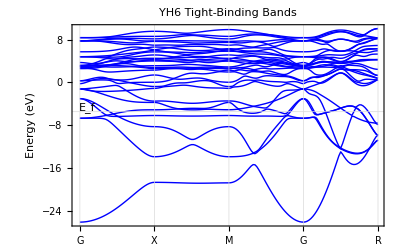

```mathematica
(*---第六步：绘图---*)
Print["正在计算 BCC 原胞能带..."];
ListLinePlot[
Transpose[energyData],
PlotRange->{Min[energyData], Max[energyData]},
Frame->True,
Axes->False,(*关键：禁用坐标轴，防止 y=0 的实线出现*)
GridLines->{Table[i*segments+1,{i,0,4}],{Ef}},
GridLinesStyle->{Directive[Gray,Dashed],Directive[Red,Thick,Dashed]},
FrameTicks->{{Automatic,None},{Table[{(i-1)*segments+1,labels[[i]]},{i,Length[labels]}],None}},
FrameLabel->{None,"Energy (eV)"},
PlotStyle->Directive[Thick,Blue],
PlotLabel->"YH6 Tight-Binding Bands",
Epilog->{Style[Text["\!\(\*SubscriptBox[\(E\), \(f\)]\)",{5,Ef+0.8}],Red,14,Bold]}
]
```